### Harmonic oscillator/optical cavity

```mathematica
W = DiagonalMatrix[Table[γ (Nb+1)(n+1),{n,0,nmax-1}],1] + DiagonalMatrix[Table[γ Nb n,{n,1,nmax}],-1]//mf;
```

(0 | (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Nb γ | 0 | 2 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 Nb γ | 0 | 3 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 Nb γ | 0 | 4 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4 Nb γ | 0 | 5 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 Nb γ | 0 | 6 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 6 Nb γ | 0 | 7 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 7 Nb γ | 0 | 8 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 Nb γ | 0 | 9 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 Nb γ | 0 | 10 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 Nb γ | 0 | 11 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 Nb γ | 0 | 12 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 Nb γ | 0 | 13 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 Nb γ | 0 | 14 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 Nb γ | 0 | 15 (1+Nb) γ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15 Nb γ | 0 | 16 (1+Nb) γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 Nb γ | 0 | 17 (1+Nb) γ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 Nb γ | 0 | 18 (1+Nb) γ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 Nb γ | 0 | 19 (1+Nb) γ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19 Nb γ | 0 | 20 (1+Nb) γ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 20 Nb γ | 0)

```mathematica
Clear[W];
Nb = 1.5;
γ = 1.0;
nmax = 50;
(*W = Table[KroneckerDelta[m,n+1] γ(Nb+1)(n+1)+KroneckerDelta[m,n-1] γ Nb n,{n,0,nmax},{m,0,nmax}]//mf;*)
W = DiagonalMatrix[Table[γ (Nb+1)(n+1),{n,0,nmax-1}],1] + DiagonalMatrix[Table[γ Nb n,{n,1,nmax}],-1];
result = {#⟦1⟧,#⟦2⟧-1}&/@Gillespie[W,10,550];
```

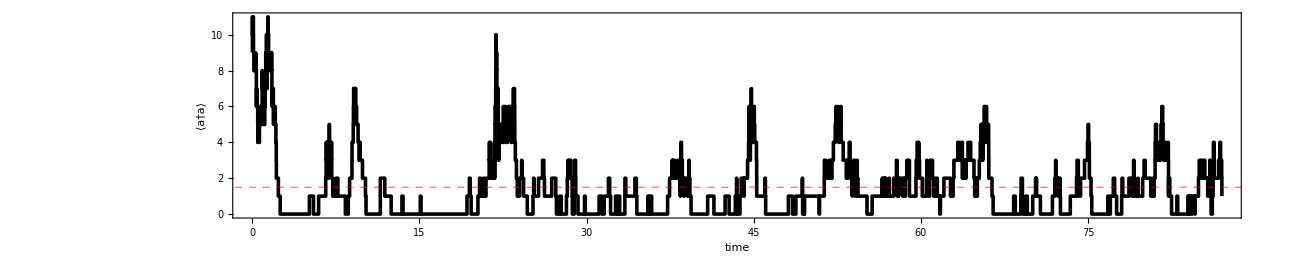

```mathematica
ListLinePlot[result,
InterpolationOrder->0,
AspectRatio->1/5,
ImageSize->1000,
PlotStyle->Directive[Black,Thickness[0.002]],
GridLines->{None,{Nb}},
GridLinesStyle->Directive[Red,Dashed,Thick],
FrameLabel->{"time","⟨a†a⟩"}
]
```

### Qubit

```mathematica
LoadPauliMatrices[]
```

Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, GMAT[θ,ϕ]

```mathematica
vg = {0,1};
ve = {1,0};
σp.vg//mf;
```

(1
0)

```mathematica
out[ve,vg]
```

{{0,1},{0,0}}

```mathematica
ρ=({{p, q}, {qs, 1-p}});
Eigenvalues[ρ]//cf
```

{1/2 (1-√((1-2 p)^2+4 q qs)),1/2 (1+√((1-2 p)^2+4 q qs))}

```mathematica
D1=σm.ρ.σp-1/2 σp.σm.ρ-1/2 ρ.σp.σm//cf//mf;
```

(-p | -q/2
-qs/2 | p)

```mathematica
D2=σp.ρ.σm-1/2 σm.σp.ρ-1/2 ρ.σm.σp//cf//mf;
```

(1-p | -q/2
-qs/2 | -1+p)

```mathematica
Clear[ω]
H = ω/2 σz;
ℋ=-ⅈ ℂ[H,ρ]//cf//mf;
```

(0 | -ⅈ q ω
ⅈ qs ω | 0)

```mathematica
nb=1/(ⅇ^βω-1);
nb/(2nb+1)//cf
```

1/(1+ⅇ^βω)

```mathematica
Tr[σp.σm.(ℋ + γ (𝒩+1) D1 + γ 𝒩 D2)]//cf
```

(𝒩-p (1+2 𝒩)) γ

```mathematica
V = g σx;
𝒱=-ⅈ ℂ[V,ρ]//cf//mf;
```

(ⅈ g (q-qs) | ⅈ g (-1+2 p)
ⅈ g (1-2 p) | -ⅈ g (q-qs))

```mathematica
eqs=(ℋ+𝒱 + γ (𝒩+1) D1 + γ 𝒩 D2);
eq1 = eqs[[1,1]]//cf
eq2 = eqs[[1,2]]//cf
eq3 = eqs[[2,1]]//cf
```

ⅈ g (q-qs)+(𝒩-p (1+2 𝒩)) γ

1/2 ⅈ (g (-2+4 p)+ⅈ q (γ+2 𝒩 γ+2 ⅈ ω))

ⅈ g (1-2 p)-1/2 qs (γ+2 𝒩 γ-2 ⅈ ω)

```mathematica
sol=Solve[{eq1==0,eq2==0,eq3==0},{p,q,qs}]//cf
```

{{p→(𝒩+(4 g^2)/(8 g^2+(γ+2 𝒩 γ)^2+4 ω^2))/(1+2 𝒩),q→-(2 ⅈ g (γ+2 𝒩 γ-2 ⅈ ω))/((1+2 𝒩) (8 g^2+(γ+2 𝒩 γ)^2+4 ω^2)),qs→(2 ⅈ g (γ+2 𝒩 γ+2 ⅈ ω))/((1+2 𝒩) (8 g^2+(γ+2 𝒩 γ)^2+4 ω^2))}}

```mathematica
sol/.𝒩->0//cf
```

{{p→(4 g^2)/(8 g^2+γ^2+4 ω^2),q→(g (-2 ⅈ γ-4 ω))/(8 g^2+γ^2+4 ω^2),qs→(2 ⅈ g (γ+2 ⅈ ω))/(8 g^2+γ^2+4 ω^2)}}

### Vectorization

```mathematica
LoadPauliMatrices[]
```

Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, GMAT[θ,ϕ]

```mathematica
Clear[ω,γ,Nb]
```

```mathematica
H = ω σp.σm;
```

```mathematica
jumpOps = {σm,σp};
rates = {γ (Nb+1),γ Nb};
```

```mathematica
ℒ = Liouvillian[H,jumpOps,rates]//Simplify//mf;
```

(-((1+Nb) γ) | 0 | 0 | Nb γ
0 | -1/2 (1+2 Nb) γ+ⅈ ω | 0 | 0
0 | 0 | -1/2 (1+2 Nb) γ-ⅈ ω | 0
(1+Nb) γ | 0 | 0 | -Nb γ)

```mathematica
ρ = SteadyState[ℒ]//mf;
```

(Nb/(1+2 Nb) | 0
0 | (1+Nb)/(1+2 Nb))

```mathematica
Tr[σp.σm.ρ]
```

Nb/(1+2 Nb)

### Harmonic oscillator

```mathematica
LoadBosonicOperators[nmax = 30];
ω = 1.0;
ϵ = 0.3;
Nb  = 1.5;
γ = 1.0;
H = ω a†.a + ϵ (a+a†);
jumpOps={a,a†};
rates = {γ (Nb+1),γ Nb};
ℒ = Liouvillian[H,jumpOps,rates];
```

```mathematica
ρ = SteadyState[ℒ];
```

```mathematica
Tr[a.ρ]
```

-0.23999-0.120005 ⅈ

```mathematica
Tr[a†.a.ρ]
```

1.57199+0. ⅈ

```mathematica
ρ//A
```

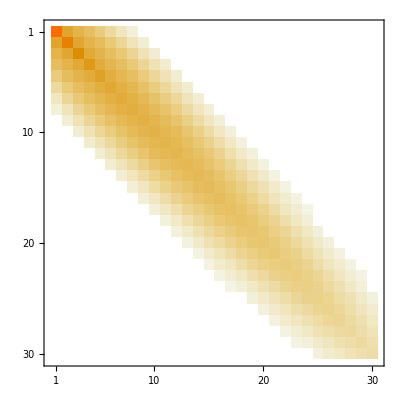

```mathematica
ρ//Abs//MatrixPlot
```

```mathematica
ℒ//mf;
```

```mathematica
ψ0 = Basis[nmax,1];
ρ0 = out[ψ0,ψ0];
```

```mathematica
Δt = 0.5;
ρt = Vec[ρ0];
ρs = Table[ρt = MatrixExp[ℒ Δt,ρt],{50}];
```

```mathematica
Dimensions[ρs]
```

{50,900}

```mathematica
Clear[r]
```

```mathematica
list=Table[Tr[a†.a.Unvec[r]],{r,ρs}]//Chop
```

{0.607456,0.999478,1.24856,1.40079,1.48783,1.53271,1.55231,1.55858,1.55933,1.55902,1.55963,1.56157,1.56439,1.56741,1.57003,1.5719,1.57294,1.57327,1.57313,1.57274,1.57231,1.57197,1.57176,1.57168,1.57171,1.57179,1.57189,1.57197,1.57203,1.57205,1.57205,1.57204,1.57202,1.572,1.57199,1.57198,1.57198,1.57198,1.57199,1.57199,1.57199,1.57199,1.572,1.572,1.57199,1.57199,1.57199,1.57199,1.57199,1.57199}

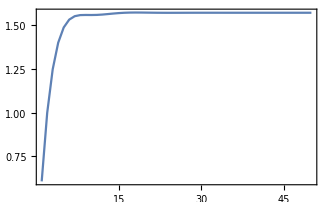

```mathematica
ListLinePlot[list,PlotRange->All]
```